# Shape 1: a near-spherical ellipsoid

## Response tensors, steady states and trajectories of a triaxial ellipsoid close to a sphere, in a uniform temperature gradient without a trap

This is the first notebook in a series asking which simple particle shape has the chirality needed for circular orbits. The physics follows the corrected notes (v22). The gas–surface stress of Eq. (50) is integrated over the particle surface. This gives the complete linear response about the centre of mass (CoM), (F, τ) = -ℛ·(∇ln T, v, ω), with blocks f_th, f_drag, B, T_th, B^ᵀ and T_drag. The temperature field is a uniform gradient ∇ln T = -G Ẑ (hot below), with no trap. The shared machinery lives in ShapeLevitation.wl next to this notebook.

Results in brief. (1) The ellipsoid is centrosymmetric, so T_th = 0 and B = 0 exactly, to all orders in the deformation. (2) To first order in ε, f_th, f_drag and T_drag are diagonal in the principal axes, with the closed forms of Section 4. (3) Nothing ever torques the particle, so every orientation is an equilibrium (neutral). (4) At levitation a tilted ellipsoid glides in a straight line at speed ≈1/5(4 - 3a)ε|e_1 - e_3|sin2θ Mg/ξ_0, up to 1.5 mm/s for the defaults. (5) There is no spin and no orbit: the orbital radius is infinite and there is no period.

## 1. Setup

```mathematica
ClearAll["Global`*"];
shapesDir=Quiet@Check[NotebookDirectory[],$Failed];If[!StringQ[shapesDir],shapesDir=Environment["SHAPES_DIR"]];
Get[FileNameJoin[{shapesDir,"ShapeLevitation.wl"}]];
$verifications={};
record[ref_,claim_,status_,detail_]:=(AppendTo[$verifications,{ref,claim,status,detail}];VR[ref,claim,status,detail]);
VR/:MakeBoxes[VR[ref_,claim_,status_,detail_],fmt_]:=ToBoxes[Panel[Column[{Row[{Style[status,Bold,If[status=="VERIFIED",Darker[Green],Red]],"   ",Style[ref,Bold],":  ",claim}],If[detail==="",Nothing,detail]}]],fmt];
check[ref_String,claim_String,test_,detail_:""]:=record[ref,claim,If[TrueQ[test],"VERIFIED","DISCREPANCY"],detail];
zeroQ[expr_]:=AllTrue[Flatten[{Simplify[expr]}],PossibleZeroQ];
sci[x_]:=If[x==0,"0",Module[{e=Floor[Log10[Abs[N[x]]]]},ToString[NumberForm[N[x]/10^e,{3,2}]]<>"e"<>ToString[e]]];
num[x_,d_:4]:=If[x!=0&&(Abs[x]<10^-3||Abs[x]>=10^5),sci[x],ToString[NumberForm[N[x],d]]];
tf[m_]:=TraditionalForm[MatrixForm[m]];
dispT[m_]:=If[DiagonalMatrixQ[m]&&!zeroQ[m],Column[Append[Table[Row[{"(",i,",",i,")   ",TraditionalForm[m[[i,i]]]}],{i,3}],"(off-diagonal entries = 0)"]],tf[m]];
n={x,y,z};
gas=gasModel[];ell=20*^-6;rhoP=1000.;
```

## 2. The shape

Lengths are in units of the mean radius l. The body is the ellipsoid with semi-axes a_i = 1 + ε e_i along the body axes x, y, z. Its surface is r = l R(n̂)n̂, where n̂ = (x, y, z) is the unit direction. The Mathematica definition used throughout is:

```mathematica
a1=1+epse1;a2=1+epse2;a3=1+epse3;
Rellipsoid[{x_,y_,z_}]:=1/Sqrt[x^2/a1^2+y^2/a2^2+z^2/a3^2];
defaults={eps->1/10,e1->1,e2->0,e3->-1};
Rnum[nn_List]:=Rellipsoid[nn]/.defaults;
Row[{"R(n) = ",TraditionalForm[Rellipsoid[n]],"      defaults: ",defaults,"   (semi-axes 1.1, 1.0, 0.9)"}]
```

R(n) = 1/(√(x^2/(e1 eps+1)^2+y^2/(e2 eps+1)^2+z^2/(e3 eps+1)^2))      defaults: {eps→1/10,e1→1,e2→0,e3→-1}   (semi-axes 1.1, 1.0, 0.9)

The defaults give a triaxial body, 10% longer along x and 10% shorter along z. The symbolic engine needs a radius that equals 1 identically at ε = 0. On the unit sphere, x^2 + y^2 + z^2 = 1, the same surface is R = [1 + ∑_i (a_i^-2 - 1)n_i^2]^(-1/2). The first check confirms the two forms agree. The free-molecule stress model assumes a convex body (no element shadows another), which the second check confirms. The last check tests the numerical quadrature against the exact mass and inertia of an ellipsoid.

```mathematica
Rsph=1/Sqrt[1+(a1^-2-1)x^2+(a2^-2-1)y^2+(a3^-2-1)z^2];
pt=makeParticle[Rnum,ell,rhoP,gas];
Module[{Mex,Iex,A=N[{a1,a2,a3}/.defaults]},Mex=4Pi/3rhoPell^3Times@@A;Iex=Mexell^2/5DiagonalMatrix[{A[[2]]^2+A[[3]]^2,A[[1]]^2+A[[3]]^2,A[[1]]^2+A[[2]]^2}];Column[{check["surface","the regular form equals the ellipsoid on the unit sphere",zeroQ[(Rsph-Rellipsoid[n])/.z->Sqrt[1-x^2-y^2]]],check["convex","the default body is convex (smallest principal curvature > 0)",convexityMargin[Rnum]>0,"smallest principal curvature = "<>num[convexityMargin[Rnum]]<>" / ell"],check["quadrature","numerical mass, CoM and inertia match the exact ellipsoid",Abs[pt["M"]/Mex-1]<10^-8&&Norm[pt["com"]]<10^-12ell&&Norm[pt["I"]-Iex]/Norm[Iex]<10^-8,"M = "<>num[pt["M"]]<>" kg,  I/(M ell^2) = "<>ToString[Round[Diagonal[pt["I"]]/(pt["M"]ell^2),10.^-4]]]}]]
```

✓ VERIFIED    surface:   the regular form equals the ellipsoid on the unit sphere

✓ VERIFIED    convex:   the default body is convex (smallest principal curvature > 0)
smallest principal curvature = 0.7439 / ell

✓ VERIFIED    quadrature:   numerical mass, CoM and inertia match the exact ellipsoid
M = 3.32e-11 kg,  I/(M ell^2) = {0.362, 0.404, 0.442}

## 3. Diagram

The diagram shows the default body, coloured by R - 1 (red is long, blue is short), with its body axes. The black dot is the geometric centre, which here is also the CoM and the centre of force. The symmetry group is D_(2h): three mirror planes, three two-fold axes, and inversion through the centre.

```mathematica
Row[{shapeDiagram[Rnum,{0,0,0},PlotLabel->"ellipsoid, semi-axes (1.1, 1.0, 0.9) ell"],shapeDiagram[Rnum,{0,0,0},ViewPoint->{0,0,5},PlotLabel->"top view (down z)"]}]
```

-Graphics3D--Graphics3D-

## 4. The four tensors

The symbolic engine expands the surface normal, the area element and every stress kernel in ε. It then integrates the resulting polynomials in n̂ exactly with the sphere moments ∮ x^a y^b z^c dΩ. Results are in natural units: f_th in γ_0, f_drag in ξ_0, T_th in γ_0 l, T_drag in c_0, and B in ξ_0 l, where γ_0, ξ_0 and c_0 are the sphere values of the notes. The accommodation coefficient a is kept general.

```mathematica
shE=symbolicShape[Rsph,n,eps,1,1,"Accommodation"->a];
bl=Map[FullSimplify,shE["blocks"],{3}];
Grid[{{"f_th / gamma0 :",dispT[bl["f_th"]]},{"f_drag / xi0 :",dispT[bl["f_drag"]]},{"T_th / (gamma0 l) :",dispT[bl["T_th"]]},{"T_drag / c0 :",dispT[bl["T_drag"]]},{"B / (xi0 l) :",dispT[bl["B"]]}},Alignment->{Left,Center},Spacings->{1,1.5},Frame->All]
```

f_th / gamma0 : | (1,1)   1/5 (2 (2 a-1) e1 eps-2 (a-3) eps (e2+e3)+5)
(2,2)   1-2/5 eps ((a-3) e1-2 a e2+(a-3) e3+e2)
(3,3)   1-2/5 eps ((a-3) (e1+e2)-2 a e3+e3)
(off-diagonal entries = 0)
f_drag / xi0 : | (1,1)   1/5 ((16 a eps (2 e1-e2-e3))/(π a+8)-2 e1 eps+6 e2 eps+6 e3 eps+5)
(2,2)   2/5 eps (-(8 a (e1-2 e2+e3))/(π a+8)+3 e1-e2+3 e3)+1
(3,3)   2/5 eps (-(8 a (e1+e2-2 e3))/(π a+8)+3 e1+3 e2-e3)+1
(off-diagonal entries = 0)
T_th / (gamma0 l) : | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
T_drag / c0 : | (1,1)   4/5 eps (e1+2 (e2+e3))+1
(2,2)   4/5 eps (2 e1+e2+2 e3)+1
(3,3)   4/5 eps (2 (e1+e2)+e3)+1
(off-diagonal entries = 0)
B / (xi0 l) : | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

With E ≡ e_1 + e_2 + e_3 and i labelling the principal axis, the four tensors to first order in ε are:

f_th = γ_0 diag[1 + (2ε)/5((3 - a)E - (4 - 3a)e_i)]

f_drag = ξ_0 diag[1 + (2ε)/5(3E - 4 e_i + (8a(3 e_i - E))/(8 + π a))]

T_th = 0   (exactly, to all orders)

T_drag = c_0 diag[1 + (4ε)/5(2E - e_i)] ,    B = B^ᵀ = 0

The isotropic parts are just the size change: an ellipsoid with all e_i = e is a sphere of radius 1 + ε e, so γ_0, ξ_0 ∝ l^2 gain 2ε e and c_0 ∝ l^4 gains 4ε e. The anisotropic parts are what matter for the motion. For full accommodation (a = 1), f_th is smaller along a long axis, by 2/5 ε e_i γ_0. The thermophoretic anisotropy is proportional to 4 - 3a, which is 5 √π/√h times C_n - C_t (the normal minus the tangential heat-flux coefficient of Eq. 50). T_drag/c_0 does not depend on a.

```mathematica
Column[{check["f_th","f_th = gamma0 diag[1 + (2 eps/5)((3 - a) E - (4 - 3 a) e_i)]",zeroQ[bl["f_th"]-DiagonalMatrix[Table[1+2eps/5((3-a)(e1+e2+e3)-(4-3a){e1,e2,e3}[[i]]),{i,3}]]]],check["f_drag","f_drag = xi0 diag[1 + (2 eps/5)(3E - 4 e_i + 8a(3 e_i - E)/(8 + pi a))]",zeroQ[bl["f_drag"]-DiagonalMatrix[Table[1+2eps/5(3(e1+e2+e3)-4{e1,e2,e3}[[i]]+8a(3{e1,e2,e3}[[i]]-(e1+e2+e3))/(8+Pia)),{i,3}]]]],check["T_drag","T_drag = c0 diag[1 + (4 eps/5)(2E - e_i)], independent of a",zeroQ[bl["T_drag"]-DiagonalMatrix[Table[1+4eps/5(2(e1+e2+e3)-{e1,e2,e3}[[i]]),{i,3}]]]],check["T_th, B","T_th = B = B^T = 0 at this order",zeroQ[{bl["T_th"],bl["B"],bl["Bt"]}]]}]
```

✓ VERIFIED    f_th:   f_th = γ0 diag[1 + (2 ε/5)((3 - a) E - (4 - 3 a) e_i)]

✓ VERIFIED    f_drag:   f_drag = ξ0 diag[1 + (2 ε/5)(3E - 4 e_i + 8a(3 e_i - E)/(8 + π a))]

✓ VERIFIED    T_drag:   T_drag = c0 diag[1 + (4 ε/5)(2E - e_i)], independent of a

✓ VERIFIED    T_th, B:   T_th = B = B^T = 0 at this order

Why T_th and B vanish exactly. Under inversion through the centre (r → -r), forces and velocities (polar vectors) change sign but torques and angular velocities (axial vectors) do not. A body that is its own inversion image can therefore have no polar-to-axial coupling: T_th (torque per gradient) and B (force per angular velocity) must vanish identically. The next check confirms this with the full numerical quadrature of the exact ellipsoid at finite ε. It also compares the quadrature with the first-order formulas at small ε, where the error should shrink like ε^2.

```mathematica
Module[{bn=pt["blocks"],sym1,err},sym1[e_]:=Module[{p=makeParticle[Function[nn,Rellipsoid[nn]/.{eps->e,e1->1,e2->0,e3->-1}],ell,rhoP,gas],s},s=shE["blocks"]/.{a->1,eps->e,e1->1,e2->0,e3->-1};Max[Norm[p["blocks"]["f_th"]/p["gamma0"]-s["f_th"]],Norm[p["blocks"]["f_drag"]/p["xi0"]-s["f_drag"]],Norm[p["blocks"]["T_drag"]/p["c0"]-s["T_drag"]]]];err={sym1[0.01],sym1[0.02]};Column[{check["centrosymmetry","exact ellipsoid (eps = 0.1): T_th and B vanish to quadrature precision",Norm[bn["T_th"]]/(pt["gamma0"]ell)<10^-12&&Norm[bn["B"]]/(pt["xi0"]ell)<10^-12,"|T_th|/(gamma0 l) = "<>sci[Norm[bn["T_th"]]/(pt["gamma0"]ell)]<>",  |B|/(xi0 l) = "<>sci[Norm[bn["B"]]/(pt["xi0"]ell)]],check["first order","quadrature minus first-order formulas scales as eps^2",3.5<err[[2]]/err[[1]]<4.5,"max error "<>sci[err[[1]]]<>" at eps = 0.01 and "<>sci[err[[2]]]<>" at eps = 0.02"]}]]
```

✓ VERIFIED    centrosymmetry:   exact ellipsoid (ε = 0.1): T_th and B vanish to quadrature precision
|T_th|/(γ0 l) = 5.11e-17,  |B|/(ξ0 l) = 1.61e-16

✓ VERIFIED    first order:   quadrature minus first-order formulas scales as ε^2
max error 4.34e-4 at ε = 0.01 and 1.74e-3 at ε = 0.02

The numbers for the default particle (l = 20 μm, ρ_p = 1 g/cm.b3, air at 5 Torr and 300 K, a = 1), from the exact quadrature:

```mathematica
Grid[{{"gamma0 (N m)",ScientificForm[pt["gamma0"],4],"f_th/gamma0",tf[Round[pt["blocks"]["f_th"]/pt["gamma0"],10.^-4]]},{"xi0 (N s/m)",ScientificForm[pt["xi0"],4],"f_drag/xi0",tf[Round[pt["blocks"]["f_drag"]/pt["xi0"],10.^-4]]},{"c0 (N m s)",ScientificForm[pt["c0"],4],"T_drag/c0",tf[Round[pt["blocks"]["T_drag"]/pt["c0"],10.^-4]]},{"M (kg)",ScientificForm[pt["M"],4],"T_th","0"},{"M/xi0 (ms)",num[1000pt["M"]/pt["xi0"]],"I_zz/c0 (ms)",num[1000pt["I"][[3,3]]/pt["c0"]]}},Frame->All,Alignment->Left]
```

gamma0 (N m) | 1.421×10^-11 | f_th/gamma0 | (0.9603 | 0. | 0.
0. | 0.9954 | 0.
0. | 0. | 1.0403)
xi0 (N s/m) | 8.459×10^-9 | f_drag/xi0 | (0.9278 | 0. | 0.
0. | 0.9927 | 0.
0. | 0. | 1.0755)
c0 (N m s) | 1.215×10^-18 | T_drag/c0 | (0.93 | 0. | 0.
0. | 1.0434 | 0.
0. | 0. | 1.0882)
M (kg) | 3.318×10^-11 | T_th | 0
M/xi0 (ms) | 3.922 | I_zz/c0 (ms) | 4.828

## 5. Steady states: neutral orientation and gliding

Rotation. A steady spin ω = Ωu about the vertical needs a real, non-zero eigenvalue of T_drag^-1 T_th (notes Sec. 2.2). Here T_th = 0, so the only rotational motion is the decay of any initial spin, and every orientation is an equilibrium. Nothing selects an orientation.

Translation. Let u be the lab vertical expressed in the body frame. At rest the body-frame force balance is f_drag v = G f_th u - Mgu. Levitation fixes G by u·v = 0, and the horizontal velocity that remains is a glide. To first order in ε only the anisotropy of f_th enters (notes Eq. 43); the drag anisotropy is multiplied by γ_0 G - Mg = O(ε):

v_⊥ = Mg/ξ_0 [(f_th/γ_0 - I) u]_⊥ = -(2(4 - 3a))/5 ε Mg/ξ_0 [diag(e_i) u]_⊥ ,    |v_⊥| = (4 - 3a)/5 ε |e_1 - e_3| |sin2θ| Mg/ξ_0

The second form is for a tilt θ of the vertical within the x–z plane, u = (sinθ, 0, cosθ). The glide is fastest at 45° between the longest and shortest axes and vanishes when a principal axis is vertical. The exact glide is computed below from the quadrature tensors for every orientation (hoverDrift), and compared with the formula.

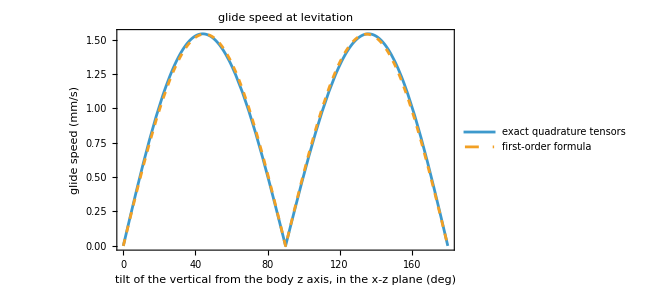

```mathematica
glideLO[th_]:=(4-3gas["a"])/5(1/10)Abs[1-(-1)]Abs[Sin[2th]]pt["M"]$gEarth/pt["xi0"];
glideExact[th_]:=hoverDrift[pt,{Sin[th],0,Cos[th]}]["speed"];
Column[{Plot[{1000glideExact[thDegree],1000glideLO[thDegree]},{th,0,180},PlotStyle->{Thick,Dashed},Frame->True,FrameLabel->{"tilt of the vertical from the body z axis, in the x-z plane (deg)","glide speed (mm/s)"},PlotLegends->{"exact quadrature tensors","first-order formula"},ImageSize->480,PlotLabel->"glide speed at levitation"],check["glide","at 45 deg the glide speed matches the first-order formula to O(eps)",Abs[glideExact[45Degree]/glideLO[45Degree]-1]<0.15,"exact "<>num[1000glideExact[45Degree]]<>" mm/s, first order "<>num[1000glideLO[45Degree]]<>" mm/s"],check["no torque","a gliding ellipsoid feels no torque at any orientation",Max[Table[Norm[hoverDrift[pt,{Sin[t]Cos[p],Sin[t]Sin[p],Cos[t]}]["torque"]],{t,0.1,3,0.4},{p,0,6,0.7}]]<10^-12pt["gamma0"]ellpt["G0"]]}]
```

✓ VERIFIED    glide:   at 45 deg the glide speed matches the first-order formula to O(ε)
exact 1.54 mm/s, first order 1.539 mm/s

✓ VERIFIED    no torque:   a gliding ellipsoid feels no torque at any orientation

Over all orientations the glide speed forms a map on the sphere of directions u. It vanishes at the six principal directions and peaks midway between the longest and shortest axes.

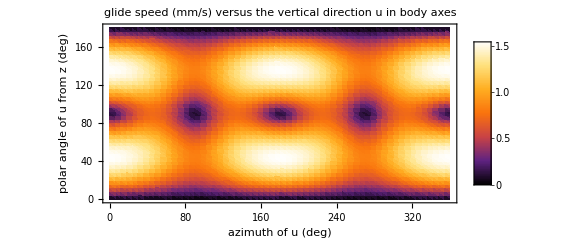

```mathematica
ListDensityPlot[Flatten[Table[{p,t,1000hoverDrift[pt,{Sin[tDegree]Cos[pDegree],Sin[tDegree]Sin[pDegree],Cos[tDegree]}]["speed"]},{t,0,180,4},{p,0,360,6}],1],ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"azimuth of u (deg)","polar angle of u from z (deg)"},ImageSize->480,PlotLabel->"glide speed (mm/s) versus the vertical direction u in body axes",AspectRatio->1/2]
```

## 6. Simulated trajectories

The simulator integrates the full nonlinear rigid-body equations with the complete 6×9 response, gravity at the CoM, and the uniform gradient (no trap). The first run starts at rest with the vertical at 45° in the x–z plane, at that orientation's levitation gradient. The second run starts at the same orientation with a 400 rad/s spin about the vertical. The spin decays within a few milliseconds. It leaves the particle turned about the vertical by about 100°, and also re-tilted a little, because the anisotropic rotational drag couples the spin into the tilt. The particle then keeps this orientation, and the glide direction turns with it: the orientation is neutral.

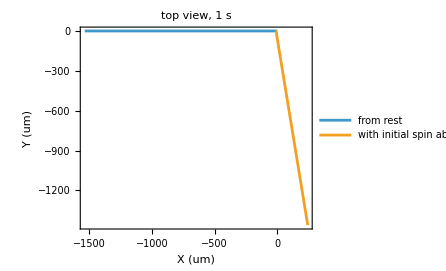
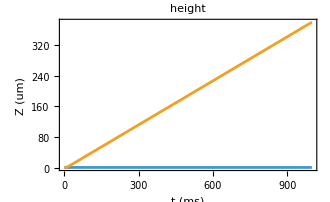

```mathematica
u45={Sin[45Degree],0,Cos[45Degree]};hd45=hoverDrift[pt,u45];
run1=simulate[pt,hd45["G"],qFromTo[u45,{0,0,1}],{0,0,0},1.];
run2=simulate[pt,hd45["G"],qFromTo[u45,{0,0,1}],400u45,1.];
uLab[st_]:=Transpose[quatR[st[[7;;10]]]].{0,0,1};
Module[{ts=Subdivide[0.,1.,400],s1,s2},s1=run1["state"]/@ts;s2=run2["state"]/@ts;Column[{Row[{ListLinePlot[{10^6s1[[All,1;;2]],10^6s2[[All,1;;2]]},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (um)","Y (um)"},PlotLegends->Placed[{"from rest","with initial spin about Z"},Below],PlotLabel->"top view, 1 s",ImageSize->330,PlotRange->All,Axes->False],ListLinePlot[{Transpose[{1000ts,10^6s1[[All,3]]}],Transpose[{1000ts,10^6s2[[All,3]]}]},Frame->True,FrameLabel->{"t (ms)","Z (um)"},PlotLabel->"height",ImageSize->330,PlotRange->All]}],check["straight line","run 1: orientation constant and the CoM glides in a straight line at the predicted velocity",Norm[uLab[s1[[-1]]]-u45]<10^-6&&Norm[s1[[-1,4;;6]]-quatR[s1[[-1,7;;10]]].hd45["v_body"]]<10^-6Norm[hd45["v_body"]],"glide speed "<>num[1000Norm[s1[[-1,4;;5]]]]<>" mm/s (predicted "<>num[1000hd45["speed"]]<>" mm/s), vertical velocity "<>sci[s1[[-1,6]]]<>" m/s"],check["neutral","run 2: the spin decays and leaves the body in a new orientation that it keeps; the glide direction turns with it",Norm[s2[[-1,11;;13]]]<10^-6&&VectorAngle[s1[[-1,4;;5]],s2[[-1,4;;5]]]/Degree>20&&Norm[uLab[s2[[-1]]]-uLab[run2["state"][0.5]]]<10^-8,"glide direction turned by "<>num[VectorAngle[s1[[-1,4;;5]],s2[[-1,4;;5]]]/Degree]<>" deg; tilt changed by "<>num[VectorAngle[uLab[s2[[-1]]],u45]/Degree]<>" deg (T_drag is anisotropic); speed "<>num[1000Norm[s2[[-1,4;;5]]]]<>" mm/s; final |omega| = "<>sci[Norm[s2[[-1,11;;13]]]]<>" rad/s"]}]]
```

✓ VERIFIED    straight line:   run 1: orientation constant and the CoM glides in a straight line at the predicted velocity
glide speed 1.54 mm/s (predicted 1.54 mm/s), vertical velocity -1.20e-16 m/s

✓ VERIFIED    neutral:   run 2: the spin decays and leaves the body in a new orientation that it keeps; the glide direction turns with it
glide direction turned by 99.82 deg; tilt changed by 7.58 deg (T_drag is anisotropic); speed 1.491 mm/s; final |ω| = 1.12e-13 rad/s

Run 1 stays at constant height. In run 2 the spin also nudges the tilt slightly (the rotational drag is anisotropic), so the levitation gradient no longer matches exactly and the particle drifts slowly in height; a trap would hold it. The animation shows run 1: the body keeps its orientation and slides sideways (toward -X). The body is drawn 3 times larger than the displacement scale, and the grey line is the CoM path.

```mathematica
With[{mesh=bodyMesh[Rnum],states=Table[run1["state"][t],{t,0.,1.,0.01}]},Manipulate[Module[{st=states[[k]],x},x=10^6st[[1;;3]];Graphics3D[{drawBody[mesh,x,quatR[st[[7;;10]]],60],If[k>1,{Gray,Thick,Line[10^6states[[1;;k,1;;3]]]},Nothing]},PlotRange->{{-1700,150},{-150,150},{-150,150}},BoxRatios->{5,1,1},Lighting->"Neutral",Axes->True,AxesLabel->{"X (um)","Y","Z"},PlotLabel->Row[{"t = ",10(k-1)," ms"}],ImageSize->600]],{{k,1,"frame (10 ms steps)"},1,101,1,ControlType->Animator,AnimationRunning->False},SaveDefinitions->True]]
```

## 7. Orbital radius and period

Not applicable. The ellipsoid has no thermophoretic torque, so it has no steady spin (Ω = 0). Its levitated motion is a straight-line glide (or a hover when a principal axis is vertical). The orbital radius is infinite and there is no orbital period. The glide direction is fixed by whatever orientation the particle happens to have.

## 8. Summary

```mathematica
Column[{Row[{"checks: ",Length[$verifications],"  (",Count[$verifications[[All,3]],"VERIFIED"]," verified)"}],Grid[Prepend[$verifications[[All,1;;3]],Style[#,Bold]&/@{"item","statement","result"}],Frame->All,Alignment->Left,Background->{None,{LightGray}}]}]
```

checks: 13  (13 verified)
item | statement | result
surface | the regular form equals the ellipsoid on the unit sphere | VERIFIED
convex | the default body is convex (smallest principal curvature > 0) | VERIFIED
quadrature | numerical mass, CoM and inertia match the exact ellipsoid | VERIFIED
f_th | f_th = gamma0 diag[1 + (2 eps/5)((3 - a) E - (4 - 3 a) e_i)] | VERIFIED
f_drag | f_drag = xi0 diag[1 + (2 eps/5)(3E - 4 e_i + 8a(3 e_i - E)/(8 + pi a))] | VERIFIED
T_drag | T_drag = c0 diag[1 + (4 eps/5)(2E - e_i)], independent of a | VERIFIED
T_th, B | T_th = B = B^T = 0 at this order | VERIFIED
centrosymmetry | exact ellipsoid (eps = 0.1): T_th and B vanish to quadrature precision | VERIFIED
first order | quadrature minus first-order formulas scales as eps^2 | VERIFIED
glide | at 45 deg the glide speed matches the first-order formula to O(eps) | VERIFIED
no torque | a gliding ellipsoid feels no torque at any orientation | VERIFIED
straight line | run 1: orientation constant and the CoM glides in a straight line at the predicted velocity | VERIFIED
neutral | run 2: the spin decays and leaves the body in a new orientation that it keeps; the glide direction turns with it | VERIFIED

Shape. Rellipsoid[{x_, y_, z_}] := 1/Sqrt[x^2/a1^2 + y^2/a2^2 + z^2/a3^2] with a_i = 1 + ε e_i; defaults ε = 0.1, e = (1, 0, -1).

Tensors. f_th, f_drag and T_drag are diagonal in the principal axes, with the O(ε) forms of Section 4. T_th = B = 0 exactly, because the body is centrosymmetric.

Motion. There is no torque, so the orientation is neutral and any spin decays. At levitation a tilted ellipsoid glides in a straight line at up to 1.5 mm/s for the defaults, fastest when the vertical lies midway between the longest and shortest axes.

Orbit. None: R = ∞, no period. An ellipsoid is achiral, and more strongly it is centrosymmetric, so it cannot turn a vertical gradient into a torque. Shape 2 adds a CoM offset, and Shape 3 adds odd harmonics.